```mathematica
(* =========================================================*)ClearAll["Global`*"];

(* =========================================================*)
(*1. CORE MODEL PRIMITIVES*)
(* =========================================================*)

tau[α_,λ_]:=λ/(1-α);
delta[α_,λ_]:=Exp[-1/tau[α,λ]];

eps0[α_,w_,λ_]:=tau[α,λ] Log[2/(1+Exp[-1/tau[α,λ]])]-w;
eps1[α_,w_,λ_]:=-tau[α,λ] Log[2/(1+Exp[1/tau[α,λ]])]-w;

BfromEps[α_,w_,x_,λ_]:=Exp[(x+w)/tau[α,λ]];

kStar[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{d=delta[α,λ]},-((d+1) B-2)/(2 d B^2-(d+1) B)];

PHint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ],d=delta[α,λ]},1/(1+k d B)];

PLint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ]},1/(1+k B)];

PHx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ],x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x<x0,1,x>x1,0,True,PHint[α,B,λ]]];

PLx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ],x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x<x0,1,x>x1,0,True,PLint[α,B,λ]]];

Px[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=(PHx[α,w,x,λ]+PLx[α,w,x,λ])/2;

KL[p_?NumericQ,q_?NumericQ]:=Which[p==0||p==1,0,q==0||q==1,0,True,p Log[p/q]+(1-p) Log[(1-p)/(1-q)]];

MIx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{ph,pl,p},ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
p=(ph+pl)/2;
1/2 KL[ph,p]+1/2 KL[pl,p]];

(* =========================================================*)
(*2. USER UTILITY AND WELFARE*)
(* =========================================================*)

Ueq[α_?NumericQ,w_?NumericQ,λ_?NumericQ][x_?NumericQ]:=Module[{x0,x1,ph,pl,mi,t},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
t=tau[α,λ];
Which[x<x0,1/2-w,(*always buy,no information acquired*)x>x1,x,(*never buy,outside option*)True,ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
mi=MIx[α,w,x,λ];
1/2 (ph (1-w)+pl (-w)+(2-ph-pl) x)-t mi]];
ClearAll[EqPolicy];

EqPolicy[λ_?NumericQ]:=EqPolicy[λ]=Quiet[SolveJoint[λ]];
lambdaVals={0.10,0.20,0.30,0.50,0.80};

eqUtilityCurve[λ_?NumericQ,step_:0.01]:=Module[{sol,αStar,wStar},sol=EqPolicy[λ];
αStar=sol["Alpha"];
wStar=sol["w"];
Table[{x,Ueq[αStar,wStar,λ][x]},{x,0.,1.,step}]];

eqCurves=eqUtilityCurve/@lambdaVals;
noMarketCurve=Table[{x,x},{x,0.,1.,0.01}];
frictionlessCurve=Table[{x,1/2+x/2},{x,0.,1.,0.01}];
UserWelfare[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=NIntegrate[Ueq[α,w,λ][x],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->30,AccuracyGoal->8,PrecisionGoal->8];
(* =========================================================*)(*2A.INTERIOR REGION HELPERS*)(* =========================================================*)InteriorWidthRaw[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Max[0,eps1[α,w,λ]-eps0[α,w,λ]];

InteriorWidthEffective[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Max[0,Min[1,x1]-Max[0,x0]]];

AggregateMI[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x0>=0,NIntegrate[MIx[α,w,x,λ],{x,x0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->30,AccuracyGoal->8,PrecisionGoal->8],x0<0<x1,NIntegrate[MIx[α,w,x,λ],{x,0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->30,AccuracyGoal->8,PrecisionGoal->8],True,0]];
(* =========================================================*)(*2B.REGIME CLASSIFICATION*)(* =========================================================*)Regime[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x0>=0,1,(*Case 1:full interior region*)x0<0<x1,2,(*Case 2:partial interior region*)x1<=0,3,(*Case 3:no interior region*)True,Missing["Undefined"]]];

RegimeLabel[r_]:=Switch[r,1,"Full interior",2,"Partial interior",3,"No interior",_,"Undefined"];

(* =========================================================*)
(*3. PLATFORM PROFITS*)
(* =========================================================*)

PiI[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x0>=0,(λ α)/(1-α)*NIntegrate[MIx[α,w,x,λ],{x,x0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],x0<0<x1,(λ α)/(1-α)*NIntegrate[MIx[α,w,x,λ],{x,0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],True,0]];

PiF[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x0>=0,w*NIntegrate[Px[α,w,x,λ],{x,x0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]+x0*w,x0<0<x1,w*NIntegrate[Px[α,w,x,λ],{x,0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],True,0]];

PiTotal[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=PiF[α,w,λ]+PiI[α,w,λ];

TotalWelfare[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=PiTotal[α,w,λ]+UserWelfare[α,w,λ];

(* =========================================================*)(*4. OPTIMIZATION ROUTINES*)(* =========================================================*)SolveJoint[λ_?NumericQ]:=Module[{sol,αStar,wStar,e0,e1,widthRaw,widthEff,aggMI,piI,piF,pi,reg},sol=NMaximize[{PiTotal[α,w,λ],0<=α<=0.95&&0<=w<=0.5},{α,w},Method->"NelderMead"];
αStar=α/. sol[[2]];
wStar=w/. sol[[2]];
e0=eps0[αStar,wStar,λ];
e1=eps1[αStar,wStar,λ];
widthRaw=InteriorWidthRaw[αStar,wStar,λ];
widthEff=InteriorWidthEffective[αStar,wStar,λ];
aggMI=AggregateMI[αStar,wStar,λ];
reg=Regime[αStar,wStar,λ];
piI=PiI[αStar,wStar,λ];
piF=PiF[αStar,wStar,λ];
pi=piF+piI;
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"PiI"->piI,"PiF"->piF,"Pi"->pi,"Ratio"->If[pi==0,0,piI/pi],"eps0"->e0,"eps1"->e1,"WidthRaw"->widthRaw,"WidthEffective"->widthEff,"AggregateMI"->aggMI,"Regime"->reg,"UserWelfare"->UserWelfare[αStar,wStar,λ],"TotalWelfare"->TotalWelfare[αStar,wStar,λ]|>];

(* =========================================================*)
(*5. RUN ON A λ GRID*)
(* =========================================================*)

lambdaGrid=N@Range[0.05,0.6,0.02];

jointResults=SolveJoint/@lambdaGrid;

(* =========================================================*)
(*6. EXTRACT SERIES*)
(* =========================================================*)

toSeries[data_,key_String]:=({#["Lambda"],#[key]}&)/@data;

extract=<|"AlphaJoint"->toSeries[jointResults,"Alpha"],"wJoint"->toSeries[jointResults,"w"],"PiIJoint"->toSeries[jointResults,"PiI"],"PiFJoint"->toSeries[jointResults,"PiF"],"PiJoint"->toSeries[jointResults,"Pi"],"RatioJoint"->toSeries[jointResults,"Ratio"],"eps0Joint"->toSeries[jointResults,"eps0"],"eps1Joint"->toSeries[jointResults,"eps1"],"WidthRawJoint"->toSeries[jointResults,"WidthRaw"],"WidthEffectiveJoint"->toSeries[jointResults,"WidthEffective"],"AggregateMIJoint"->toSeries[jointResults,"AggregateMI"],"RegimeJoint"->toSeries[jointResults,"Regime"],"UserWelfareJoint"->toSeries[jointResults,"UserWelfare"],"TotalWelfareJoint"->toSeries[jointResults,"TotalWelfare"]|>;

extract["LowerEffectiveJoint"]=({#[[1]],Max[#[[2]],0]}&)/@extract["eps0Joint"];

extract["UpperEffectiveJoint"]=({#[[1]],Max[#[[2]],0]}&)/@extract["eps1Joint"];

(* =========================================================*)
(*7. PLOTTING UTILITIES*)
(* =========================================================*)

plot1[key_String,ylab_]:=ListLinePlot[extract[key],AxesLabel->{"λ",ylab},PlotRange->All,PlotStyle->{Red,Thick},ImageSize->Large];

plot2[key1_String,key2_String,lab1_,lab2_]:=GraphicsRow[{ListLinePlot[extract[key1],PlotLegends->{lab1},AxesLabel->{"λ",lab1},PlotRange->All,PlotStyle->{Red,Thick},ImageSize->350],ListLinePlot[extract[key2],PlotLegends->{lab2},AxesLabel->{"λ",lab2},PlotRange->All,PlotStyle->{Red,Thick},ImageSize->350]}];
```

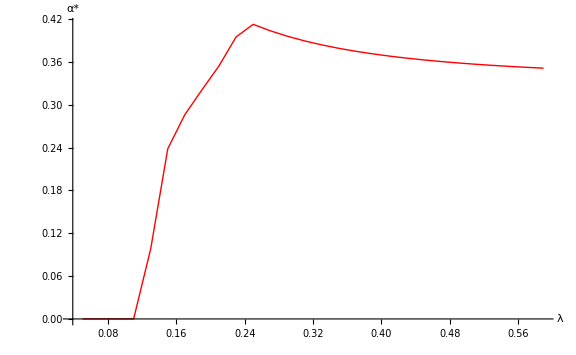

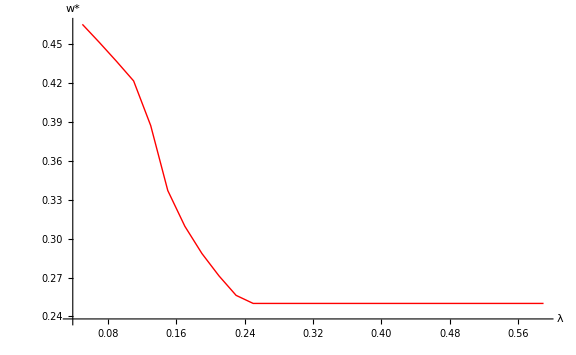

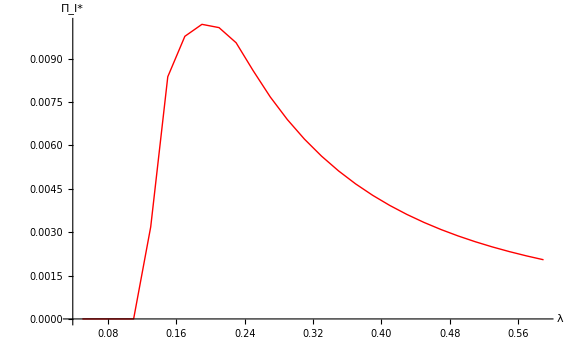

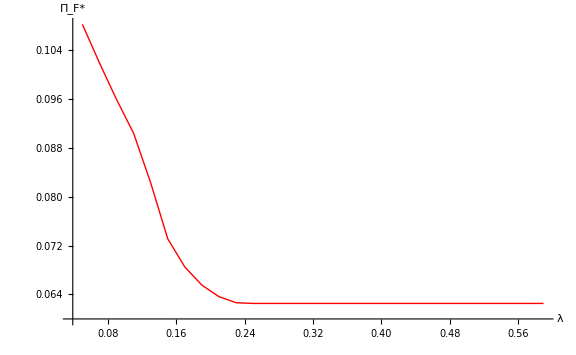

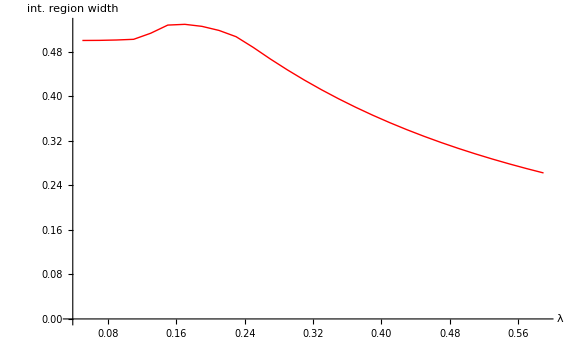

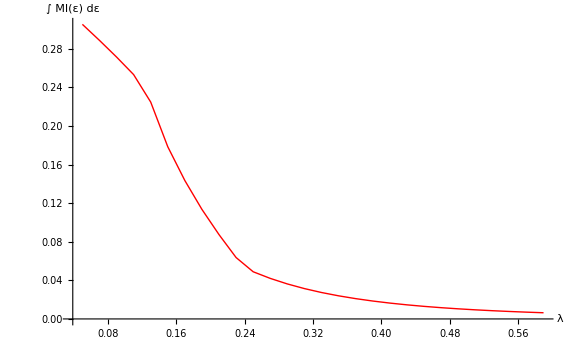

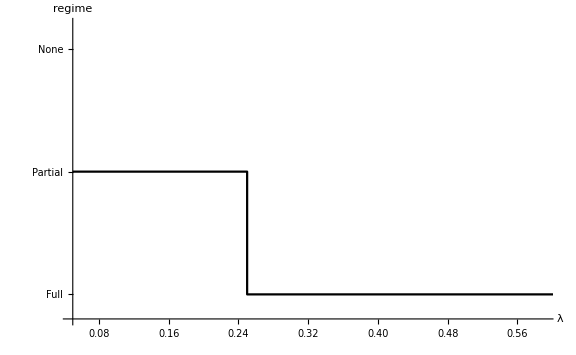

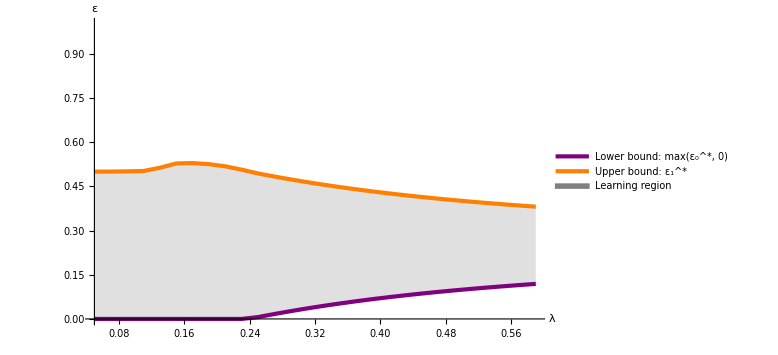

```mathematica
figAlpha=plot1["AlphaJoint","α*"]
figW=plot1["wJoint","w*"]
figPiI=plot1["PiIJoint","Π_I*"]
figPiF=plot1["PiFJoint","Π_F*"]
figPi=plot1["PiJoint","Π*"];
figRatio=plot1["RatioJoint","Π_I*/Π*"];

figWidthEff=plot1["WidthEffectiveJoint","int. region width"]
figAggMI=plot1["AggregateMIJoint","∫ MI(ε) dε"]

figRegime=ListStepPlot[{extract["RegimeJoint"]},PlotRange->{{Min[lambdaGrid],Max[lambdaGrid]},{0.8,3.2}},AxesLabel->{"λ","regime"},Ticks->{Automatic,{{1,"Full"},{2,"Partial"},{3,"None"}}},PlotStyle->{Black,Thick},ImageSize->Large]

(* =========================================================*)(*9. REGIME BANDS*)(* =========================================================*)RegimeLabel[r_]:=Switch[r,1,"Full interior",2,"Partial interior",3,"No interior",_,"Undefined"];

RegimeColor[r_]:=Switch[r,1,Directive[Opacity[0.5],LightBlue],2,Directive[Opacity[0.5],LightYellow],3,Directive[Opacity[0.5],LightRed],_,Directive[Opacity[0.08],Gray]];

RegimeIntervals[data_List]:=Module[{vals,groups,dx},vals=data;
dx=If[Length[vals]>=2,vals[[2,1]]-vals[[1,1]],0.01];
groups=SplitBy[vals,Last];
Map[Function[g,<|"Regime"->g[[1,2]],"xMin"->g[[1,1]]-dx/2,"xMax"->g[[-1,1]]+dx/2|>],groups]];

WidthPlotWithRegimesLabeled[dataWidth_List,dataRegime_List]:=Module[{bands,yMax,rects,labels,boundaries},bands=RegimeIntervals[dataRegime];
yMax=1.12 Max[dataWidth[[All,2]]];
rects=Table[{RegimeColor[bands[[i,"Regime"]]],Rectangle[{bands[[i,"xMin"]],0},{bands[[i,"xMax"]],yMax}]},{i,Length[bands]}];
labels=Table[Text[Style[RegimeLabel[bands[[i,"Regime"]]],11,Black],{(bands[[i,"xMin"]]+bands[[i,"xMax"]])/2,0.95 yMax}],{i,Length[bands]}];
boundaries=Table[{GrayLevel[0.35],AbsoluteThickness[1.2],Line[{{bands[[i,"xMin"]],0},{bands[[i,"xMin"]],yMax}}]},{i,2,Length[bands]}];
ListLinePlot[dataWidth,PlotStyle->{Red,AbsoluteThickness[3]},AxesLabel->{"λ","effective width"},

PlotRange->{{Min[lambdaGrid],Max[lambdaGrid]},{0,yMax}},ImageSize->Large,Prolog->Join[rects,boundaries,labels]]];

figInteriorBoundsFilled=Module[{fillStyle=Directive[GrayLevel[0.7],Opacity[0.4]]},Legended[ListLinePlot[{extract["LowerEffectiveJoint"],extract["UpperEffectiveJoint"]},Filling->{2->{1}},FillingStyle->fillStyle,PlotStyle->{Directive[Purple,AbsoluteThickness[3]],Directive[Orange,AbsoluteThickness[3]]},AxesLabel->{"λ","ε"},PlotRange->{{Min[lambdaGrid],Max[lambdaGrid]},{0,1}},ImageSize->Large],Placed[LineLegend[{Directive[Purple,AbsoluteThickness[3]],Directive[Orange,AbsoluteThickness[3]],Directive[GrayLevel[0.5],AbsoluteThickness[6]]},{Row[{"Lower bound: max(",Superscript[Subscript[ε,0],"*"],", 0)"}],Row[{"Upper bound: ",Superscript[Subscript[ε,1],"*"]}],"Learning region"}],Below]]]

figWidthWithRegimes=WidthPlotWithRegimesLabeled[extract["WidthEffectiveJoint"],extract["RegimeJoint"]]


extract["BuyerSurplusJoint"]=({#[[1]],#[[2]]-1/2}&)/@extract["UserWelfareJoint"];

extract["TotalSurplusJoint"]=MapThread[{#1[[1]],(#1[[2]]-1/2)+#2[[2]]}&,{extract["UserWelfareJoint"],extract["PiJoint"]}];

ListLinePlot[{extract["BuyerSurplusJoint"],extract["PiJoint"],extract["TotalSurplusJoint"]},PlotLegends->{"Buyer surplus","Platform profit","Total surplus"},AxesLabel->{"λ","Surplus"},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick],Directive[Black,Thick]},ImageSize->Large]

extract["BuyerSurplusJoint"]=({#[[1]],#[[2]]-1/2}&)/@extract["UserWelfareJoint"];

extract["TotalSurplusJoint"]=MapThread[{#1[[1]],(#1[[2]]-1/2)+#2[[2]]}&,{extract["UserWelfareJoint"],extract["PiJoint"]}];

extract["PlatformShareSurplusJoint"]=MapThread[{#1[[1]],If[#2[[2]]==0,Indeterminate,#1[[2]]/#2[[2]]]}&,{extract["PiJoint"],extract["TotalSurplusJoint"]}];

extract["BuyerShareSurplusJoint"]=MapThread[{#1[[1]],If[#2[[2]]==0,Indeterminate,#1[[2]]/#2[[2]]]}&,{extract["BuyerSurplusJoint"],extract["TotalSurplusJoint"]}];


extract["OneLine"]=({#[[1]],1}&)/@extract["BuyerShareSurplusJoint"];

buyer=extract["BuyerShareSurplusJoint"];
xMin=Min[lambdaGrid];
xMax=Max[lambdaGrid];

top=({#[[1]],1}&)/@buyer;

buyerPoly=Polygon[Join[{{buyer[[1,1]],0}},buyer,{{buyer[[-1,1]],0}}]];

platformPoly=Polygon[Join[buyer,Reverse[top]]];

(*---choose label positions---*)
xMid=(xMin+xMax)/2;

buyerVal=Interpolation[buyer][xMid];

figSurplusDivision=ListLinePlot[{buyer},Prolog->{(*filled regions*)Directive[Opacity[0.35],Blue,EdgeForm[None]],buyerPoly,Directive[Opacity[0.35],Red,EdgeForm[None]],platformPoly,(*labels*)Text[Framed[Style["Buyers",16,Bold,Blue],Background->White,FrameStyle->None,RoundingRadius->4,FrameMargins->Small],{xMid,0.5 buyerVal}],Text[Framed[Style["Platform",16,Bold, Red],Background->White,FrameStyle->None,RoundingRadius->4,FrameMargins->Small],{xMid,(1+buyerVal)/2}]},PlotStyle->{Directive[Blue,AbsoluteThickness[3]]},Axes->True,Frame->False,AxesLabel->{"λ","Share of total surplus"},PlotRange->{{xMin,xMax},{0,1}},ImageSize->{700,350},ImagePadding->{{60,20},{50,20}}]
```

```mathematica
ClearAll[Ueq];

Ueq[α_?NumericQ,w_?NumericQ,λ_?NumericQ][x_?NumericQ]:=Module[{x0,x1,ph,pl,mi,t},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
t=tau[α,λ];
Which[x<x0,1/2-w,(*always buy,no info acquisition*)x>x1,x,(*never buy,outside option*)True,ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
mi=MIx[α,w,x,λ];
1/2 (ph (1-w)+pl (-w)+(2-ph-pl) x)-t mi]];
ClearAll[SolveJointPolicy];

SolveJointPolicy[λ_?NumericQ]:=SolveJointPolicy[λ]=Module[{sol,αStar,wStar},sol=NMaximize[{PiTotal[α,w,λ],0<=α<=0.95&&0<=w<=0.5},{α,w},Method->{"NelderMead","RandomSeed"->1234},MaxIterations->120];
αStar=α/. sol[[2]];
wStar=w/. sol[[2]];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar|>];

ClearAll[EqUtilityCurveFast];

EqUtilityCurveFast[α_?NumericQ,w_?NumericQ,λ_?NumericQ,n_:120]:=Module[{t,d,x0,x1,xs,KLlocal},t=tau[α,λ];
d=Exp[-1/t];
x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
xs=N@Subdivide[0,1,n];
KLlocal[p_?NumericQ,q_?NumericQ]:=If[p<=0.||p>=1.||q<=0.||q>=1.,0.,p Log[p/q]+(1-p) Log[(1-p)/(1-q)]];
Table[Which[x<x0,{x,1/2-w},x>x1,{x,x},True,Module[{B,k,ph,pl,p,mi},B=Exp[(x+w)/t];
k=-(((d+1.) B-2.)/(2. d B^2-(d+1.) B));
ph=1./(1.+k d B);
pl=1./(1.+k B);
p=(ph+pl)/2.;
mi=1/2 KLlocal[ph,p]+1/2 KLlocal[pl,p];
{x,1/2 (ph (1-w)+pl (-w)+(2-ph-pl) x)-t mi}]],{x,xs}]];
lambdaVals={0.05,0.15,0.25 ,0.35,0.45};
LaunchKernels[];
$HistoryLength=0;
DistributeDefinitions[tau,eps0,eps1,delta,BfromEps,kStar,PHint,PLint,PHx,PLx,Px,KL,MIx,PiI,PiF,PiTotal,Ueq,SolveJointPolicy,EqUtilityCurveFast];
policies=ParallelMap[SolveJointPolicy,lambdaVals];
eqCurves=ParallelMap[EqUtilityCurveFast[#["Alpha"],#["w"],#["Lambda"],100]&,policies];
noMarketCurve=Table[{x,x},{x,0.,1.,0.01}];

figUtilityEquilibrium=ListLinePlot[Join[eqCurves,{noMarketCurve,frictionlessCurve}],PlotStyle->{Directive[RGBColor[0.95,0.85,0.30],AbsoluteThickness[1.5]],(*0.05*)Directive[RGBColor[0.95,0.65,0.15],AbsoluteThickness[1.5]],(*0.15*)
Directive[RGBColor[0.85,0.35,0.15],AbsoluteThickness[1.5]],(*0.25*)Directive[RGBColor[0.65,0.20,0.35],AbsoluteThickness[1.5]],(*0.35*)Directive[RGBColor[0.35,0.15,0.55],AbsoluteThickness[1.5]],(*0.45*)Directive[GrayLevel[0.45],AbsoluteThickness[2],Dashing[{0.015,0.015}]],(*no market*)Directive[GrayLevel[0.35],AbsoluteThickness[2],Dashing[{0.003,0.012}]]    (*no ads,no fee*)},PlotLegends->Placed[{Row[{"λ = 0.05"}],Row[{"λ = 0.15"}],Row[{"λ = 0.25"}],Row[{"λ = 0.35"}],Row[{"λ = 0.45"}],"no market","no ads, no fee"},LegendLayout->"Row"],AxesLabel->{"ε",Row[{"E[u(ε)]*"}]},PlotRange->{{0,1},{0,1}},ImageSize->{800,400}]
```

Placed::labpos: LegendLayout→Row is not a valid position for the placement of labels.

-Graphics-

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

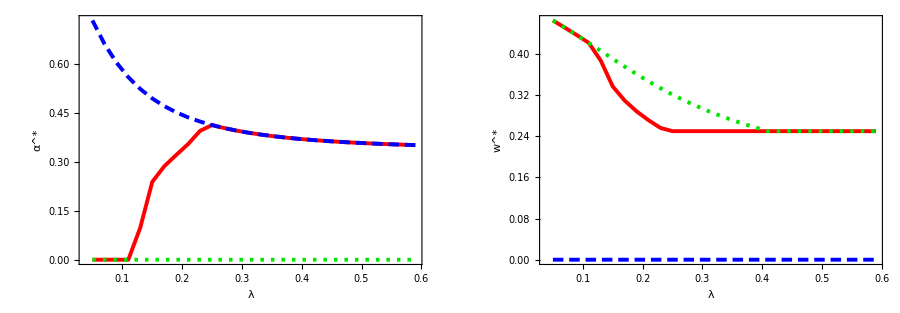
-Graphics-
-Graphics-Joint optimization-Graphics-Advertising-only-Graphics-Fee-only

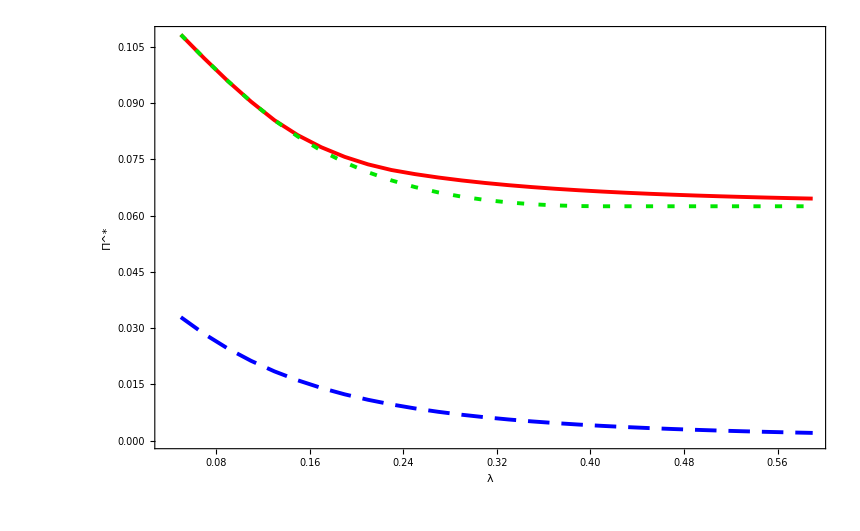
-Graphics-
-Graphics-Joint optimization-Graphics-Advertising-only-Graphics-Fee-only

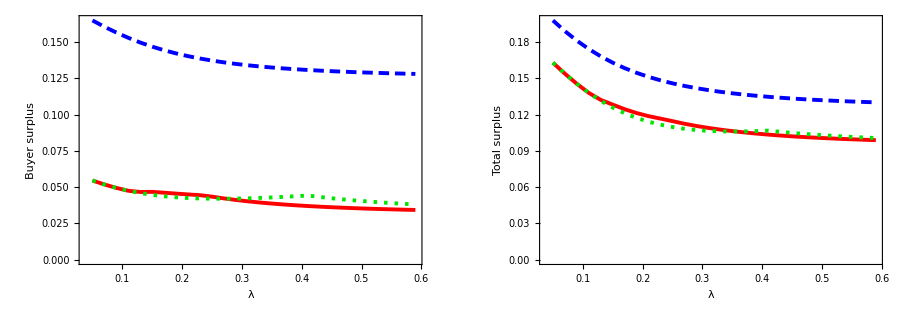
-Graphics-
-Graphics-Joint optimization-Graphics-Advertising-only-Graphics-Fee-only

C:\Users\Tereza Hofrichterová\Documents

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

-Graphics-
-Graphics-Joint optimization-Graphics-Advertising-only-Graphics-Fee-only

-Graphics-
-Graphics-Joint optimization-Graphics-Advertising-only-Graphics-Fee-only

-Graphics-
-Graphics-Joint optimization-Graphics-Advertising-only-Graphics-Fee-only

```mathematica
(* ================================================*)(*SINGLE-CHANNEL BENCHMARKS:FIGURE GENERATION*)(* ================================================*)LaunchKernels[];
$HistoryLength=0;

(*--------------------------------*)
(*0. SAFER WELFARE DEFINITIONS*)
(*--------------------------------*)

ClearAll[UserWelfareSafe,TotalWelfareSafe];

UserWelfareSafe[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Quiet@Check[NIntegrate[Ueq[α,w,λ][x],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->20,AccuracyGoal->6,PrecisionGoal->6],Indeterminate];

TotalWelfareSafe[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{pi=PiTotal[α,w,λ],uw=UserWelfareSafe[α,w,λ]},If[NumericQ[pi]&&NumericQ[uw],pi+uw,Indeterminate]];

(*--------------------------------*)
(*1. OPTIMIZATION ROUTINES*)
(*--------------------------------*)

ClearAll[SolveJointLite,SolveMedia,SolvePhysical];

SolveJointLite[λ_?NumericQ]:=SolveJointLite[λ]=Module[{sol,αStar,wStar,pi,uw,tw},sol=NMaximize[{PiTotal[α,w,λ],0<=α<=0.95&&0<=w<=0.5},{α,w},Method->{"NelderMead","RandomSeed"->1234},MaxIterations->120];
αStar=α/. sol[[2]];
wStar=w/. sol[[2]];
pi=PiTotal[αStar,wStar,λ];
uw=UserWelfareSafe[αStar,wStar,λ];
tw=If[NumericQ[uw]&&NumericQ[pi],uw+pi,Indeterminate];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"Pi"->pi,"UserWelfare"->uw,"TotalWelfare"->tw|>];

SolveMedia[λ_?NumericQ]:=SolveMedia[λ]=Module[{sol,αStar,wStar=0.,pi,uw,tw},sol=NMaximize[{PiTotal[α,0.,λ],0<=α<=0.95},α,Method->{"NelderMead","RandomSeed"->1234},MaxIterations->120];
αStar=α/. sol[[2]];
pi=PiTotal[αStar,wStar,λ];
uw=UserWelfareSafe[αStar,wStar,λ];
tw=If[NumericQ[uw]&&NumericQ[pi],uw+pi,Indeterminate];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"Pi"->pi,"UserWelfare"->uw,"TotalWelfare"->tw|>];

SolvePhysical[λ_?NumericQ]:=SolvePhysical[λ]=Module[{sol,αStar=0.,wStar,pi,uw,tw},sol=NMaximize[{PiTotal[0.,w,λ],0<=w<=0.5},w,Method->{"NelderMead","RandomSeed"->1234},MaxIterations->120];
wStar=w/. sol[[2]];
pi=PiTotal[αStar,wStar,λ];
uw=UserWelfareSafe[αStar,wStar,λ];
tw=If[NumericQ[uw]&&NumericQ[pi],uw+pi,Indeterminate];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"Pi"->pi,"UserWelfare"->uw,"TotalWelfare"->tw|>];

DistributeDefinitions[tau,eps0,eps1,delta,BfromEps,kStar,PHint,PLint,PHx,PLx,Px,KL,MIx,Ueq,PiI,PiF,PiTotal,UserWelfareSafe,TotalWelfareSafe,SolveJointLite,SolveMedia,SolvePhysical];

(*--------------------------------*)
(*2. RUN ON λ GRID*)
(*--------------------------------*)

lambdaGridSingle=N@Range[0.05,0.6,0.02];

jointSingleResults=ParallelMap[SolveJointLite,lambdaGridSingle];
mediaResults=ParallelMap[SolveMedia,lambdaGridSingle];
physicalResults=ParallelMap[SolvePhysical,lambdaGridSingle];

(*--------------------------------*)
(*3. SERIES EXTRACTION*)
(*--------------------------------*)

ClearAll[toSeries,cleanSeries];

toSeries[data_,key_String]:=({#["Lambda"],#[key]}&)/@data;

cleanSeries[data_]:=Select[data,MatchQ[#,{_?NumericQ,_?NumericQ}]&];

extractSingle=<|"AlphaJoint"->cleanSeries@toSeries[jointSingleResults,"Alpha"],"AlphaMedia"->cleanSeries@toSeries[mediaResults,"Alpha"],"AlphaPhysical"->cleanSeries@toSeries[physicalResults,"Alpha"],"wJoint"->cleanSeries@toSeries[jointSingleResults,"w"],"wMedia"->cleanSeries@toSeries[mediaResults,"w"],"wPhysical"->cleanSeries@toSeries[physicalResults,"w"],"PiJoint"->cleanSeries@toSeries[jointSingleResults,"Pi"],"PiMedia"->cleanSeries@toSeries[mediaResults,"Pi"],"PiPhysical"->cleanSeries@toSeries[physicalResults,"Pi"],"UserWelfareJoint"->cleanSeries@toSeries[jointSingleResults,"UserWelfare"],"UserWelfareMedia"->cleanSeries@toSeries[mediaResults,"UserWelfare"],"UserWelfarePhysical"->cleanSeries@toSeries[physicalResults,"UserWelfare"],"TotalWelfareJoint"->cleanSeries@toSeries[jointSingleResults,"TotalWelfare"],"TotalWelfareMedia"->cleanSeries@toSeries[mediaResults,"TotalWelfare"],"TotalWelfarePhysical"->cleanSeries@toSeries[physicalResults,"TotalWelfare"]|>;

(*Buyer surplus=buyer welfare-E[epsilon]=buyer welfare-1/2*)
extractSingle["BuyerSurplusJoint"]=({#[[1]],#[[2]]-1/2}&)/@extractSingle["UserWelfareJoint"];

extractSingle["BuyerSurplusMedia"]=({#[[1]],#[[2]]-1/2}&)/@extractSingle["UserWelfareMedia"];

extractSingle["BuyerSurplusPhysical"]=({#[[1]],#[[2]]-1/2}&)/@extractSingle["UserWelfarePhysical"];

(*Total surplus=buyer surplus+platform profit*)
extractSingle["TotalSurplusJoint"]=MapThread[{#1[[1]],#1[[2]]+#2[[2]]}&,{extractSingle["BuyerSurplusJoint"],extractSingle["PiJoint"]}];

extractSingle["TotalSurplusMedia"]=MapThread[{#1[[1]],#1[[2]]+#2[[2]]}&,{extractSingle["BuyerSurplusMedia"],extractSingle["PiMedia"]}];

extractSingle["TotalSurplusPhysical"]=MapThread[{#1[[1]],#1[[2]]+#2[[2]]}&,{extractSingle["BuyerSurplusPhysical"],extractSingle["PiPhysical"]}];
(*--------------------------------*)(*COMMON STYLES*)(*--------------------------------*)jointStyle=Directive[Red,AbsoluteThickness[2.8]];
mediaStyle=Directive[Blue,AbsoluteThickness[2.8],Dashing[{0.018,0.01}]];
physicalStyle=Directive[Darker[Green,0.1],AbsoluteThickness[2.8],Dashing[{0.006,0.012}]];

(*Manual one-row legend:guaranteed one row*)
legendItem[style_,text_]:=Row[{Graphics[{style,Line[{{0,0},{1,0}}]},PlotRange->{{0,1},{-0.5,0.5}},ImageSize->{32,10},Axes->False],Spacer[6],Style[text,13,FontFamily->"Helvetica"]}];

legendRow=Row[{legendItem[jointStyle,"Joint optimization"],Spacer[20],legendItem[mediaStyle,"Advertising-only"],Spacer[20],legendItem[physicalStyle,"Fee-only"]},Alignment->Center];

(*Frame labels behave much better than AxesLabel for cropping*)
baseOpts={PlotRange->All,ImageSize->{420,300},LabelStyle->Directive[13],Frame->True,Axes->False,RotateLabel->True,ImagePadding->{{95,20},{35,10}}};

wideOpts={PlotRange->All,ImageSize->{860,360},LabelStyle->Directive[13],Frame->True,Axes->False,RotateLabel->True,ImagePadding->{{95,20},{35,10}}};

(*Put legend close to the plot*)
withBottomLegend[plot_]:=Column[{plot,legendRow},Spacings->0.1,Alignment->Center];

(*--------------------------------*)
(*5. FIGURE:POLICIES*)
(*--------------------------------*)

figPoliciesSingle=withBottomLegend@GraphicsRow[{ListLinePlot[{extractSingle["AlphaJoint"],extractSingle["AlphaMedia"],extractSingle["AlphaPhysical"]},PlotStyle->{jointStyle,mediaStyle,physicalStyle},FrameLabel->{Style["λ",12],Style[Superscript["α","*"],12]},Evaluate@baseOpts],ListLinePlot[{extractSingle["wJoint"],extractSingle["wMedia"],extractSingle["wPhysical"]},PlotStyle->{jointStyle,mediaStyle,physicalStyle},FrameLabel->{Style["λ",12],Style[Superscript["w","*"],12]},Evaluate@baseOpts]},Spacings->20,ImageSize->900];

(*--------------------------------*)
(*6. FIGURE:PROFITS*)
(*--------------------------------*)

figProfitSingle=withBottomLegend@ListLinePlot[{extractSingle["PiJoint"],extractSingle["PiMedia"],extractSingle["PiPhysical"]},PlotStyle->{jointStyle,mediaStyle,physicalStyle},FrameLabel->{Style["λ",12],Style[Superscript["Π","*"],12]},Evaluate@wideOpts];
(*--------------------------------*)
(*7. FIGURE:WELFARE*)
(*--------------------------------*)
figWelfareSingle=withBottomLegend@GraphicsRow[{ListLinePlot[{extractSingle["BuyerSurplusJoint"],extractSingle["BuyerSurplusMedia"],extractSingle["BuyerSurplusPhysical"]},PlotStyle->{jointStyle,mediaStyle,physicalStyle},FrameLabel->{Style["λ",12],Style["Buyer surplus",12]},Evaluate@baseOpts],ListLinePlot[{extractSingle["TotalSurplusJoint"],extractSingle["TotalSurplusMedia"],extractSingle["TotalSurplusPhysical"]},PlotStyle->{jointStyle,mediaStyle,physicalStyle},FrameLabel->{Style["λ",12],Style["Total surplus",12]},Evaluate@baseOpts]},Spacings->20,ImageSize->900];

(*--------------------------------*)
(*8. DISPLAY*)
(*--------------------------------*)

figPoliciesSingle
figProfitSingle
figWelfareSingle

(*--------------------------------*)
(*9. EXPORT*)
(*--------------------------------*)

Export["policies_single.pdf",figPoliciesSingle];
Export["profit_single.pdf",figProfitSingle];
Export["welfare_single.pdf",figWelfareSingle];

Directory[]
```

{{0.46533,0.},{0.45128,0.},{0.436756,0.},{0.421674,0.},{0.387218,0.0981392},{0.337092,0.23824},{0.309512,0.286057},{0.288491,0.32071},{0.27122,0.354309},{0.256219,0.394804},{0.25,0.412446},{0.25,0.403434},{0.25,0.395809},{0.25,0.389311},{0.25,0.383738},{0.25,0.378927},{0.25,0.37475},{0.25,0.371104},{0.25,0.367905},{0.25,0.365085},{0.25,0.362587},{0.25,0.360366},{0.25,0.358383},{0.25,0.356605},{0.25,0.355006},{0.25,0.353564},{0.25,0.352258},{0.25,0.351072}}

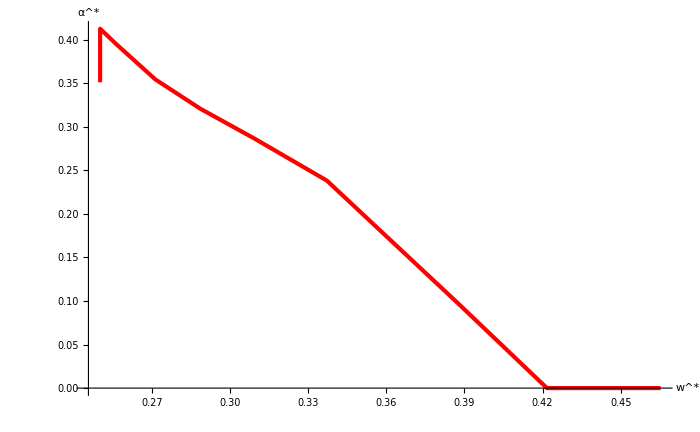

```mathematica
alphaWCurve=MapThread[{#1[[2]],#2[[2]]}&,{extract["wJoint"], extract["AlphaJoint"]}]

figAlphaW=ListLinePlot[alphaWCurve,PlotStyle->{Directive[Red,AbsoluteThickness[3]]},AxesLabel->{Style[Superscript["w","*"],12],Style[Superscript["α","*"],12]},PlotRange->All,ImageSize->{700,450},LabelStyle->Directive[13],ImagePadding->{{80,20},{50,15}}]
```